```mathematica
data = {{0.5,0.0160916},{0.2,0.00385546},{0.1,0.00103098},{0.05,0.000263436},{0.0333333,0.000117377},{0.025,6.60578*10^(-5)}}
```

{{0.5,0.0160916},{0.2,0.00385546},{0.1,0.00103098},{0.05,0.000263436},{0.0333333,0.000117377},{0.025,0.0000660578}}

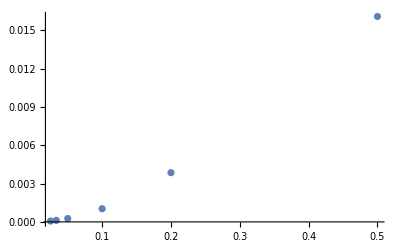

FittedModel[0.000346542+0.0635877 x^2]

```mathematica
dataplot = ListPlot[data, PlotRange->All]
lm = LinearModelFit[data, {x^2},x]
```

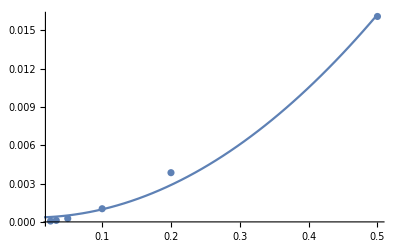

```mathematica
Show[dataplot, Plot[lm[x],{x,0,0.5}]]
```

```mathematica
data2 = {{0.5,0.444162},{0.2,0.641158},{0.1,0.566837},{0.05,0.392653},{0.0333333,0.297912},{0.025,0.242133},{0.0166667,.176004},{0.0125,0.138647},{0.01,0.114786}}
```

{{0.5,0.444162},{0.2,0.641158},{0.1,0.566837},{0.05,0.392653},{0.0333333,0.297912},{0.025,0.242133},{0.0166667,0.176004},{0.0125,0.138647},{0.01,0.114786}}

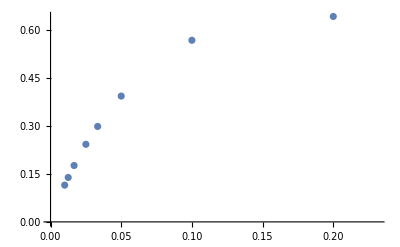

```mathematica
dataplot2 = ListPlot[data2]
```